# Plane Partition

### Author

Eric W. Weisstein
December 2, 2008

This notebook downloaded from http://mathworld.wolfram.com/notebooks/Combinatorics/PlanePartition.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/PlanePartition.html.

©2008 Wolfram Research, Inc. except for portions noted otherwise

### Additional Authors

Generation code by Wouter Meeussen
http://users.pandora.be/Wouter.Meeussen/PlanePartitions.txt
December 28, 2003

### Code

```mathematica
coversQ[parent_,child_]:=And[Length[parent]>=Length[child],Min[Take[parent,Length@child]-child]>=0]

planepartitionQ[par_]:=MatchQ[par,{{___Integer}..}]&&If[Length[par]>1,And@@MapThread[coversQ,{Drop[par,-1],Rest[par]}],True]

PlanePartitions[n_Integer]:=Module[{l1,l2,l3,l4,z,w},
l1=z@@@IntegerPartitions[n];
l2=l1/.k_Integer/;(k>1):>w@@IntegerPartitions[k];
l3=l2/.z[x_w,y:(1...)]:>Thread[z[x,y],w]/.
z[x__w]:>Outer[z,x]/.z[x__w,y:(1...)]:>Outer[z,x,Sequence@@({y}/. 1->w[1])]/.w->Sequence;
l4=l3/.z[x___List,y:(1..)]:>z[x,Sequence@@Transpose[{{y}}]]/.z->List;Cases[Union[l4],_?planepartitionQ]
]
```

## 3-D Diagram

```mathematica
PlanePartitionDiagram[l_List]:=Module[{i,j,k},
Graphics3D[
Table[Cuboid[{j,-i,k}],
{i,Length[l]},
{j,Length[l[[i]]]},
{k,l[[i,j]]}
]
]
]
```

```mathematica
Show[PlanePartitionDiagram[{{5,4,2,1,1},{3,2},{2,2}}]]
```

⁃Graphics3D⁃

## Enumeration

A000219

```mathematica
Length/@PlanePartitions/@Range[20]//Timing
```

{45.4971,{1,3,6,13,24,48,86,160,282,500,859,1479,2485,4167,6879,11297,18334,29601,47330,75278}}

```mathematica
PlanePartitions[2]
```

{{{2}},{{1,1}},{{1},{1}}}

```mathematica
(ColumnForm/@PlanePartitions[#]&)/@Range[4]//ColumnForm
```

{{1}}
{{2},{1,1},{1}
{1}}
{{3},{2,1},{1,1,1},{2}
{1},{1,1}
{1},{1}
{1}
{1}}
{{4},{2,2},{3,1},{2,1,1},{1,1,1,1},{2}
{2},{3}
{1},{1,1}
{1,1},{2,1}
{1},{1,1,1}
{1},{2}
{1}
{1},{1,1}
{1}
{1},{1}
{1}
{1}
{1}}

### Generating Function

```mathematica
Product[(1-x^k)^k,{k,∞}]
```

∏_k^∞ (1-x^k)^k

```mathematica
Series[1/Product[(1-x^k)^k,{k,50}],{x,0,10}]
```

1+x+3 x^2+6 x^3+13 x^4+24 x^5+48 x^6+86 x^7+160 x^8+282 x^9+500 x^10+O[x]^11

```mathematica
seq=CoefficientList[Series[1/Product[(1-x^k)^k,{k,100}],{x,0,20}],x]
```

{1,1,3,6,13,24,48,86,160,282,500,859,1479,2485,4167,6879,11297,18334,29601,47330,75278}

```mathematica
FindLinearRecurrence[Drop[seq,2]]//Head//Timing
```

{0.006769,FindLinearRecurrence}

```mathematica
FindSequenceFunction[seq,n]//Head//Timing
```

{40.8056,FindSequenceFunction}

```mathematica
FindGeneratingFunction[seq,x]//Head//Timing
```

{40.3889,FindGeneratingFunction}

### Recurrence

RSolve[{(∑_k^n a[-k+n] DivisorSigma[2,k])/n,a[0]==1},a[n],n]

```mathematica
a[0]:=1
a[n_]:=a[n]=1/n Sum[a[n-k]DivisorSigma[2,k],{k,n}]
```

```mathematica
Array[a,20]
```

{1,3,6,13,24,48,86,160,282,500,859,1479,2485,4167,6879,11297,18334,29601,47330,75278}

```mathematica
RSolve[{1/n Sum[a[n-k]DivisorSigma[2,k],{k,n}],a[0]==1},a[n],n]
```

RSolve::deqn: Equation or list of equations expected instead of (∑_k^n a[-k+n] DivisorSigma[2,k])/n in the first argument {(∑_k^n a[-k+n] DivisorSigma[2,k])/n,a[0]==1}.

```mathematica
RecurrenceTable[{1/n Sum[a[n-k]DivisorSigma[2,k],{k,n}],a[0]==1},a,{n,5}]
```

RecurrenceTable::deqn: Equation or list of equations expected instead of (∑_k^n a[-k+n] DivisorSigma[2,k])/n in the first argument {(∑_k^n a[-k+n] DivisorSigma[2,k])/n,a[0]==1}.

RecurrenceTable[{(∑_k^n a[-k+n] DivisorSigma[2,k])/n,a[0]==1},a,{n,5}]

```mathematica
Series[Exp[Sum[DivisorSigma[2,n] x^n/n,{n,10}]],{x,0,10}]
```

1+x+3 x^2+6 x^3+13 x^4+24 x^5+48 x^6+86 x^7+160 x^8+282 x^9+500 x^10+O[x]^11

```mathematica
Sum[DivisorSigma[2,n] x^n/n,{n,∞}]
```

∑_n^∞ (x^n DivisorSigma[2,n])/n

```mathematica
CoefficientList[Series[Exp[Sum[DivisorSigma[2,n] x^n/n,{n,20}]],{x,0,20}],x]
```

{1,1,3,6,13,24,48,86,160,282,500,859,1479,2485,4167,6879,11297,18334,29601,47330,75278}

## Asymptotic

```mathematica
Limit[Zeta[3]^(7/36)/2^(11/36)/Sqrt[3*Pi]/Glaisher*E^(3*Zeta[3]^(1/3)*(n/2)^(2/3)+1/12)/n^(25/36)/a[n],n->Infinity]==1
```

lim_(n→∞) (ⅇ^(1/12+(3 n^(2/3) Zeta[3]^(1/3))/2^(2/3)) Zeta[3]^(7/36))/(2^(11/36) Glaisher n^(25/36) √(3 π) a[n])==1

```mathematica
seq=CoefficientList[Series[1/Product[(1-x^k)^k,{k,100}],{x,0,30}],x]
```

{1,1,3,6,13,24,48,86,160,282,500,859,1479,2485,4167,6879,11297,18334,29601,47330,75278,118794,186475,290783,451194,696033,1068745,1632658,2483234,3759612,5668963}

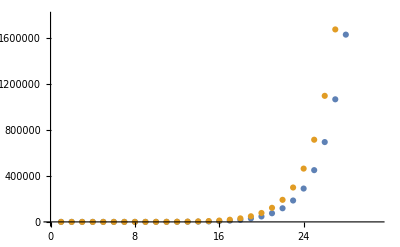

```mathematica
ListPlot[{seq,
Table[Zeta[3]^(7/36)/2^(11/36)/Sqrt[3*Pi]/Glaisher*E^(3*Zeta[3]^(1/3)*(n/2)^(2/3)+1/12)/n^(25/36),{n,30}]}]
```

```mathematica
Length[seq]
```

31

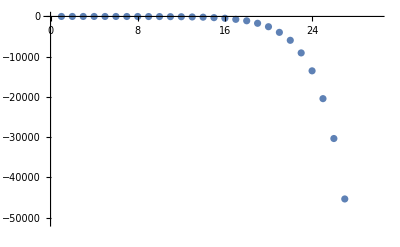

```mathematica
ListPlot[Rest@seq-
Table[Zeta[3]^(7/36)/2^(11/36)/Sqrt[3*Pi]/Glaisher*E^(3*Zeta[3]^(1/3)*(n/2)^(2/3)+1/12)/n^(25/36),{n,30}]]
```

## Young Diagrams fit in an a×b×c Box

```mathematica
BoxPartitions[a_,b_,c_]:=
Product[(i+j+k-1)/(i+j+k-2),{i,a},{j,b},{k,c}]
```

```mathematica
FullSimplify[∏_(k=1)^c (-1+i+j+k)/(-2+i+j+k)]
```

1+c/(-1+i+j)

```mathematica
FullSimplify[∏_(j=1)^b (1+c/(-1+i+j))]
```

Pochhammer[c+i,b]/Pochhammer[i,b]

```mathematica
FunctionExpand[%]
```

(Gamma[i] Gamma[b+c+i])/(Gamma[b+i] Gamma[c+i])

```mathematica
∏_(i=1)^a (Gamma[i] Gamma[b+c+i])/(Gamma[b+i] Gamma[c+i])
```

∏_(i=1)^a (Gamma[i] Gamma[b+c+i])/(Gamma[b+i] Gamma[c+i])

#### V6

```mathematica
BoxPartitions[a,b,c]
```

∏_(i=1)^a ∏_(j=1)^b ∏_(k=1)^c (-1+i+j+k)/(-2+i+j+k)

#### V7

```mathematica
BoxPartitions[a,b,c]
```

(BarnesG[1+a] BarnesG[1+b] BarnesG[1+c] BarnesG[1+b+c]^(-1+a) BarnesG[2+b+c]^-a BarnesG[1+a+b+c] (BarnesG[2+b]/(BarnesG[1+b] Gamma[1+b]))^a (BarnesG[2+c]/(BarnesG[1+c] Gamma[1+c]))^a Gamma[1+b+c]^a)/(BarnesG[1+a+b] BarnesG[1+a+c])

```mathematica
FullSimplify[BoxPartitions[a,b,c]-(BarnesG[a+1]BarnesG[b+1]BarnesG[c+1]BarnesG[a+b+c+1])/(BarnesG[a+b+1]BarnesG[a+c+1]BarnesG[b+c+1])]
```

(BarnesG[1+a] BarnesG[1+b] BarnesG[1+c] BarnesG[2+b+c]^-a BarnesG[1+a+b+c] (-BarnesG[2+b+c]^a+BarnesG[1+b+c]^a (BarnesG[2+b]/(BarnesG[1+b] Gamma[1+b]))^a (BarnesG[2+c]/(BarnesG[1+c] Gamma[1+c]))^a Gamma[1+b+c]^a))/(BarnesG[1+a+b] BarnesG[1+a+c] BarnesG[1+b+c])

```mathematica
Table[%/.{a->RandomInteger[{1,10}],b->RandomInteger[{1,10}],c->RandomInteger[{1,10}]},{100}]//Union
```

{0}

```mathematica
∏_(i=1)^a (Gamma[i] Gamma[b+c+i])/(Gamma[b+i] Gamma[c+i])
```

(BarnesG[1+a] BarnesG[1+b] BarnesG[1+c] BarnesG[1+b+c]^(-1+a) BarnesG[2+b+c]^-a BarnesG[1+a+b+c] (BarnesG[2+b]/(BarnesG[1+b] Gamma[1+b]))^a (BarnesG[2+c]/(BarnesG[1+c] Gamma[1+c]))^a Gamma[1+b+c]^a)/(BarnesG[1+a+b] BarnesG[1+a+c])

```mathematica
FullSimplify[BoxPartitions[n,n,n],n∈Integers&&n>0]
```

(BarnesG[1+n]^(3-2 n) BarnesG[2+n]^(2 n) BarnesG[1+3 n] (n!)^(-2 n))/BarnesG[1+2 n]^3

```mathematica
Table[(BarnesG[1+n]^(3-2 n) BarnesG[2+n]^(2 n) BarnesG[1+3 n] Gamma[1+n]^(-2 n))/BarnesG[1+2 n]^3,{n,10}]
```

{2,20,980,232848,267227532,1478619421136,39405996318420160,5055160684040254910720,3120344782196754906063540800,9265037718181937012241727284450000}

### In terms of Barnes G

```mathematica
BarnesG[n_Integer]:=Times@@(Factorial/@Range[n-2])
```

```mathematica
bbb[a_,b_,c_]:=g[a+1]g[b+c+a+1]/g[b+c+1]/(g[b+a+1]/g[b+1]g[c+a+1]/g[c+1])/.g->BarnesG
```

```mathematica
bbb[a,b,c]
```

(BarnesG[1+a] BarnesG[1+b] BarnesG[1+c] BarnesG[1+a+b+c])/(BarnesG[1+a+b] BarnesG[1+a+c] BarnesG[1+b+c])

```mathematica
Table[Subtract@@{bbb[a,b,c],∏_(i=1)^a (Gamma[i] Gamma[b+c+i])/(Gamma[b+i] Gamma[c+i]) }/. Thread[{a,b,c}->Table[Random[Integer,{1,10}],{3}]],{5}]
```

{0,0,0,0,0}

#### With a=b=c=n

```mathematica
bbb[n,n,n]
```

(BarnesG[1+n]^3 BarnesG[1+3 n])/BarnesG[1+2 n]^3

```mathematica
Product[(Gamma[i]Gamma[i+2n])/Gamma[i+n]^2,{i,n}]
```

∏_(i=1)^n (Gamma[i] Gamma[i+2 n])/Gamma[i+n]^2

```mathematica
Table[bbb[n,n,n],{n,10}]
```

{2,20,980,232848,267227532,1478619421136,39405996318420160,5055160684040254910720,3120344782196754906063540800,9265037718181937012241727284450000}